## Figure 6

```mathematica
SetDirectory@NotebookDirectory[];
```

### loading Stan output

PLchn - MCMC chain Pailin, WPchn - MCMC chain Wang Pha

```mathematica
PLchn=Import["PL-stan-output.csv"];
WPchn=Import["WP-stan-output.csv"];
```

```mathematica
ListParPos=38;
ChainBeg=43;
ChainEnd=1042;
```

list of the population mean parameters

```mathematica
PLchn[[ListParPos,8;;20]]
```

{N0_mean,mu_mean,sig_mean,pmr_mean,gamma_mean,ec50_mean,deadrateR_mean,deadrateT_mean,deadrateS_mean,recoverrateR_mean,recoverrateT_mean,recoverrateS_mean,recoverlag_mean}

positions of parameters in the chain

```mathematica
ParPosIndx=Thread[PLchn[[ListParPos,8;;20]]->Range[8,20]]
```

{N0_mean→8,mu_mean→9,sig_mean→10,pmr_mean→11,gamma_mean→12,ec50_mean→13,deadrateR_mean→14,deadrateT_mean→15,deadrateS_mean→16,recoverrateR_mean→17,recoverrateT_mean→18,recoverrateS_mean→19,recoverlag_mean→20}

```mathematica
ParPosition[par_,site_]:=Position[If[StringMatchQ["PL",site],PLchn[[ListParPos]],WPchn[[ListParPos]]],s_String/;StringMatchQ[s,par]][[1,1]]
```

```mathematica
PLchnDat=PLchn[[ChainBeg;;ChainEnd,All]];
WPchnDat=WPchn[[ChainBeg;;ChainEnd,All]];
```

```mathematica
Dimensions/@{PLchnDat,WPchnDat}
```

{{1000,42726},{1000,40428}}

list of the clearance time parameters in the output MCMC chain

```mathematica
PLACTpars="AS7CT."<>ToString@#&/@Range[1,20];
PLSplitACTpars="SplitCT."<>ToString@#&/@Range[1,20];
WPACTpars="AS7CT."<>ToString@#&/@Range[1,19];
WPSplitACTpars="SplitCT."<>ToString@#&/@Range[1,19];
```

function for calculating the median of the parasite clearance times from each patient in different dosing regiment and study sites

```mathematica
CT[]:=Block[{plpct,plpct2,wppct,wppct2,PLACTpars,PLSplitACTpars,WPACTpars,WPSplitACTpars},

PLACTpars="AS7CT."<>ToString@#&/@Range[1,20];
PLSplitACTpars="SplitCT."<>ToString@#&/@Range[1,20];
WPACTpars="AS7CT."<>ToString@#&/@Range[1,19];
WPSplitACTpars="SplitCT."<>ToString@#&/@Range[1,19];

plpct=(PLchnDat[[All,ParPosition[#,"PL"]]]&/@PLACTpars);
plpct2=(PLchnDat[[All,ParPosition[#,"PL"]]]&/@PLSplitACTpars);
wppct=(WPchnDat[[All,ParPosition[#,"WP"]]]&/@WPACTpars);
wppct2=(WPchnDat[[All,ParPosition[#,"WP"]]]&/@WPSplitACTpars);

{Median/@plpct,Median/@plpct2,Median/@wppct,Median/@wppct2}
];
```

```mathematica
Thread[{"Pailin every 24 hours","Pailin every 12 hours","Wang Pha every 24 hours","Wang Pha every 12 hours"}->CT[]]//TableForm
```

Pailin every 24 hours→{64,83,96,98,79,61,38,40,77,55,95,74,73,119,42,94,93,44,67,52}
Pailin every 12 hours→{61,81,93,95,78,54,35,35,75,54,92,70,71,115,37,92,87,42,66,49}
Wang Pha every 24 hours→{43,10,30,28,41,14,59,51,53,30,19,27,44,14,16,26,50,93,68}
Wang Pha every 12 hours→{38,10,19,19,29,14,57,42,45,17,16,17,39,14,15,23,45,83,61}

plotting the smooth histogram of the clearance times from each dosing regimen

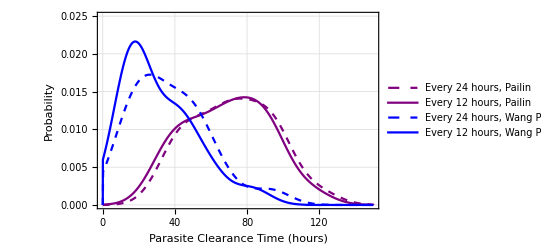

```mathematica
ctdat=CT[];
SmoothHistogram[ctdat,PlotStyle->{Directive[Dashed,Purple],Directive[Purple],Directive[Dashed,Blue],Directive[Blue]},Frame->True,GridLines->Automatic,FrameLabel->{"Parasite Clearance Time (hours)","Probability"},PlotRange->{{0,150},{0,0.025}},PlotLegends->LineLegend[{Directive[Dashed,Purple],Directive[Purple],Directive[Dashed,Blue],Directive[Blue]},{"Every 24 hours, Pailin","Every 12 hours, Pailin","Every 24 hours, Wang Pha","Every 12 hours, Wang Pha"}],LabelStyle->Directive[Bold,FontFamily->"Times New Roman"]]
```